```mathematica
ClearAll["Global`*"]
```

```mathematica
Q1=P3 μ1+p γ1 μ2;Q2=(P2 P3 P4-(-1+p) P3 γ1 (P4+γ2)+p P2 γ1 (P4+γ3))νh;Q3=(1-p) γ1 P3+k p γ1 P2+P2 P3;
P5=dh+νh;P1=γ1+μ1+dh;P2=γ2+dh;P3=γ3+μ2+dh;P4=ρ+dh;P6=dm+νm;
```

```mathematica
C0=(Ah dm^2 P1 P2 P3 P5 P6)/(a^2 b c dh Q3 νh νm);C1=(Ah dm P1 P2 P3 P4 P5 P6 (2 dm P2 Q1-a c dh Q3))/(a^2 b c dh Q3 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh) νm);C11=(Ah dm P1 P2 P3 P4 P5 P6 ((P1 P2 P3 P4+Q2) (2 dm P2 Q1-a c dh Q3)+a c P2 P4 Q1 Q3 νh))/(a^2 b c Q3 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh)^2 νm);
```

```mathematica
{b2,b1,b0}={a^2 Ah^2 c^2 dh^2 dm^2 P1^2 P2^2 P3^2 P4^2 P5^2 P6^2 Q3^2,2 a^2 Ah b c dh^2 dm P1 P2 P3 P4 P5 P6 Q3 (-(P1 P2 P3 P4+Q2) (2 dm P2 Q1-a c dh Q3)-a c P2 P4 Q1 Q3 νh) νm,a^4 b^2 c^2 dh^2 Q3^2 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh)^2 νm^2};(-b1+√(b1^2-4*b0*b2))/(2 b0);
```

```mathematica
data={a->0.1,Ah->0.5,b->0.022,c->0.24,dh->0.000000358,k->0.5,p->0.70433,γ1->0.33,γ2->1.0035,γ3->0.0357,μ1->0.000018,μ2->0.000018,νh->0.2,νm->0.083,ρ->0.0027};
ndm0=(a c dh Q3)/(P2 Q1)/.data;
ndm1=-(a c dh P4 Q3 νh)/(dh P1 P2 P3 P4+dh Q2-P2 P4 Q1 νh)/.data;
{f1,f2,f3,f4,f5}={C0,C1,C11,(-b1+√(b1^2-4*b0*b2))/(2 b0),(-b1-√(b1^2-4*b0*b2))/(2 b0)}/.data;
```

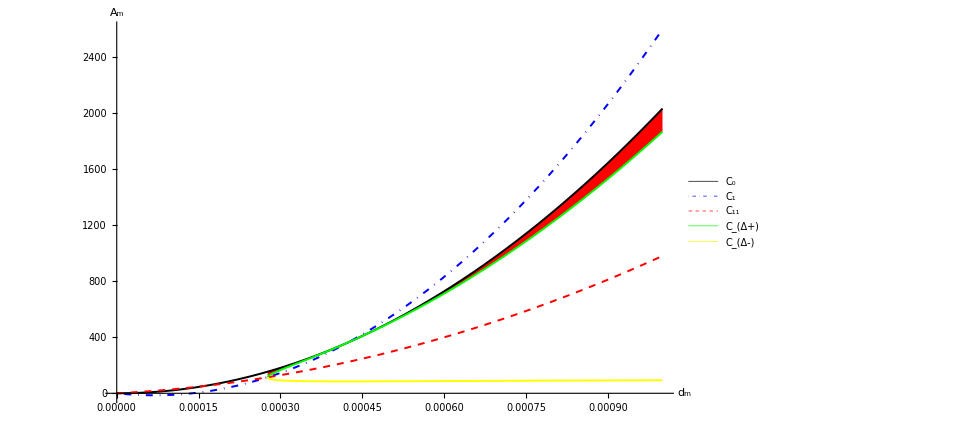

```mathematica
fig1=Plot[{f1,f2,f3,f4,f5},{dm,0,0.001},PlotLegends->Placed[LineLegend[Automatic,{"C_0","C_1","C_11","C_(Δ+)","C_(Δ-)"},LegendLayout->{"Column",1}],{0.2,0.8}],PlotStyle->{{Black,Thickness[0.002]},{Blue,DotDashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Green,Thickness[0.002]},{Yellow,Thickness[0.002]}},AxesOrigin->{0,0},AxesLabel->{"d_m","A_m"},BaseStyle->{FontFamily->"Times",FontSize->10},AxesStyle->Thickness[0.003],PlotRange->All,Filling->{1->{{4},{None,Red}}}]
```